# Polar Transform in 2D

## Environment

```mathematica
SetOptions[EvaluationNotebook[],CellContext->Notebook];
```

## Boxes

```mathematica
MakeBoxes[xSub0,StandardForm]:=SubscriptBox["x","0"];
MakeExpression[SubscriptBox["x","0"],StandardForm]:=MakeExpression["xSub0",StandardForm];
MakeBoxes[xSuper0,StandardForm]:=SuperscriptBox["x","0"];
MakeExpression[SuperscriptBox["x","0"],StandardForm]:=MakeExpression["xSuper0",StandardForm];
MakeBoxes[xSuper1,StandardForm]:=SuperscriptBox["x","1"];
MakeExpression[SuperscriptBox["x","1"],StandardForm]:=MakeExpression["xSuper1",StandardForm];
MakeBoxes[xSuper2,StandardForm]:=SuperscriptBox["x","2"];
MakeExpression[SuperscriptBox["x","2"],StandardForm]:=MakeExpression["xSuper2",StandardForm];
MakeBoxes[xPrime,StandardForm]:=SuperscriptBox[ "x",FromCharacterCode[700]];
MakeExpression[SuperscriptBox["x",FromCharacterCode[700]],StandardForm]:=MakeExpression["xPrime",StandardForm];
MakeBoxes[xPrime0,StandardForm]:=SuperscriptBox[ "x",FromCharacterCode[700]<>"0"];
MakeExpression[SuperscriptBox["x",FromCharacterCode[700]<>"0"],StandardForm]:=MakeExpression["xPrime0",StandardForm];
MakeBoxes[xPrime1,StandardForm]:=SuperscriptBox[ "x",FromCharacterCode[700]<>"1"];
MakeExpression[SuperscriptBox["x",FromCharacterCode[700]<>"1"],StandardForm]:=MakeExpression["xPrime1",StandardForm];
MakeBoxes[xPrime2,StandardForm]:=SuperscriptBox[ "x",FromCharacterCode[700]<>"2"];
MakeExpression[SuperscriptBox["x",FromCharacterCode[700]<>"2"],StandardForm]:=MakeExpression["xPrime2",StandardForm];
```

## Motion Specification

```mathematica
Subscript[x, 0]={1.5,-4.};
v={1.,8.};
```

## ODE Description of Motion

```mathematica
x[t_]={(x^1)[t],(x^2)[t]}/.First[DSolve[{{((x^1)')[t],((x^2)')[t]}==v,{(x^1)[0],(x^2)[0]}==Subscript[x, 0]},{x^1,x^2},t]];
```

## Cartesian to Polar Transforms

```mathematica
Polar[x_]:={√(∑_i^2 x⟦i⟧^2),ArcTan[x⟦1⟧,x⟦2⟧]}
Cartesian[x^ʼ:_]:={(x^ʼ)⟦1⟧ Cos[(x^ʼ)⟦2⟧],(x^ʼ)⟦1⟧ Sin[(x^ʼ)⟦2⟧]}
```

## Jacobian Matrices

```mathematica
CartesianJacobian[x_]:=D[Polar[{x^1,x^2}], {{x^1,x^2}}]/.{x^1->x⟦1⟧,x^2->x⟦2⟧};
PolarJacobian[x^ʼ:_]:=D[Cartesian[{x^ʼ1,x^ʼ2}], {{x^ʼ1,x^ʼ2}}]/.{x^ʼ1->(x^ʼ)⟦1⟧,x^ʼ2->(x^ʼ)⟦2⟧};
```

## Make Basis Vector from Cartesian Coordinates

```mathematica
makeBasis[spot_]:=(J=PolarJacobian[Polar[spot]];{{spot,{spot⟦1⟧+J⟦1⟧⟦1⟧,spot⟦2⟧+J⟦2⟧⟦1⟧}},{spot,{spot⟦1⟧+J⟦1⟧⟦2⟧,spot⟦2⟧+J⟦2⟧⟦2⟧}}});
```

## Show the Basis Vector Transform

```mathematica
polarOneForm = Table[Circle[{0, 0}, r], {r, {1, 2, 3, 4, 5}}]; 
segment = Line[{x[0.],x[1.]}]; 
milestones = Point[x /@ Range[0., 1., 0.1]]; 
Manipulate[Graphics[{polarOneForm, {Blue, segment}, {Gray, milestones}, {Red, Line[makeBasis[x[time]]]}}, PlotRange -> {{-6, 6}, {-6, 6}}, Axes -> True], 
  {time, 0., 1.}]
```

## Travel Along a Straight Line

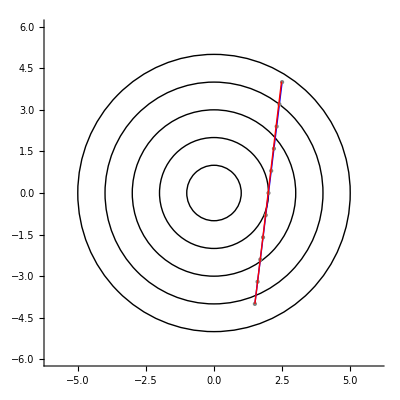

```mathematica
getPolarPoints[dλ_]:=(
cPoints={x[0.]};
pPoint=Polar[cPoints⟦1.⟧];
Do[
pPoint=pPoint+CartesianJacobian[Cartesian[pPoint]].x'[λ] dλ;
AppendTo[cPoints,Cartesian[pPoint]];,
{λ,0.,1.,dλ}];
cPoints)
Graphics[{polarOneForm,{Blue,segment},{Gray,milestones},{Red,Line[getPolarPoints[1/500]]}},PlotRange->{{-6,6},{-6,6}},Axes->True]
```

## Cartesian Distance

```mathematica
Subscript[g, c]={{1,0},{0,1}};
dx=D[x[t], t];
√(dx.Subscript[g, c].dx)
```

8.06226

## Polar Distance

```mathematica
polarDistance[dλ_] :=
(
length=0;
pPoint=Polar[x[0.]];
Do[
(
dx=CartesianJacobian[Cartesian[pPoint]].x'[λ]dλ;
r=pPoint⟦1⟧;
Subscript[g, r]={{1,0},{0,r^2}};
ds=√(dx.Subscript[g, r].dx);
length=length+ds;
pPoint = pPoint+dx;
), {λ, 0., 1., dλ}]; 
   length)
```

```mathematica
polarDistance[0.001]
```

8.07032